# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/miguel/Documents/Wolfram Mathematica/QKT/Symmetry breaking

```mathematica
LaunchKernels[8]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy];
Sz[J_]:=Sz[J]=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=Sx[J]=SparseArray[(1/2)(SM[J]+Sm[J])];
Sy[J_]:=Sy[J]=SparseArray[(1/(2I))(SM[J]-Sm[J])];
```

# Method

```mathematica
radius=1.99999;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

20272

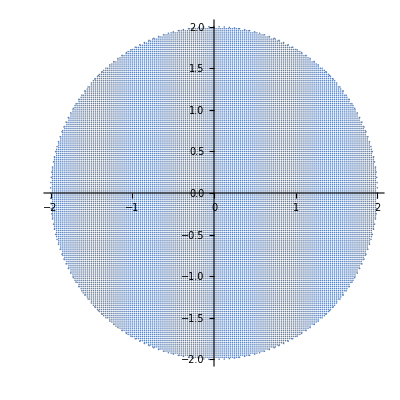

```mathematica
ListPlot[region,AspectRatio->1]
```

```mathematica
(*rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2])Sz[J]];*)
```

```mathematica
Clear[J];
J=200;
α=0.84;
τ=1;
k=20.;
```

```mathematica
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
Clear[a1,a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Quiet[Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]]
];
a1[J_Integer,theta_,phi_]:=Module[{mvals=Range[-J,J],coeffs},
Quiet[Normalize[N[Table[Binomial[2J,J+m]*(Cos[theta/2]^(J+m))*(Exp[I*phi]Sin[theta/2])^(J-m),{m,mvals}]]]]
];
```

```mathematica
flist={};
Do[
mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
AppendTo[flist,neweigenvec];
,{k,10,20,1.}];
```

```mathematica
AbsoluteTiming[coherentstates=Developer`ToPackedArray[ParallelTable[a2[J,i[[1]],i[[2]]],{i,region}]];]
```

{111.706,Null}

```mathematica
(*ParallelEvaluate[
(
iprcompiled=Compile[{{eigenvec,_Complex,2},{states,_Complex,2}},
Module[{overlaps},
overlaps=Map[Abs[Conjugate[eigenvec].#]^2&,states];
Map[Total[Abs[#]^2]&,overlaps]
]
,CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}];
)
];*)
```

```mathematica
ParallelEvaluate[
(
localstates=coherentstates;
iprcompiled=Compile[{{eigenvec,_Complex,2},{states,_Complex,2}},
Module[{overlaps},
overlaps=Map[Abs[Conjugate[eigenvec].#]^2&,states];
Map[Total[Abs[#]^2]&,overlaps]
]
,CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}];
)
];
```

```mathematica
AbsoluteTiming[data=ParallelTable[Module[{eigenvec=flist[[i]]},
iprcompiled[eigenvec,localstates]
],{i,Length[flist]}];]
```

{46.7087,Null}

```mathematica
plots=Table[ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],data[[i]]}],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",ColorFunction->"TemperatureMap",ImageSize->800],{i,Length[flist]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

## Second test

```mathematica
Clear[iprvectorized];
iprvectorized[eigenvec_,states_]:=Module[{overlaps},
overlaps=Conjugate[eigenvec].Transpose[states];
Total[Abs[overlaps]^4,{1}]
];
```

```mathematica
DistributeDefinitions[J,iprvectorized];
```

```mathematica
ParallelEvaluate[(
localstates=coherentstates;
iprcompile=Compile[{{eigenvec,_Complex,2},{states,_Complex,2}},
iprvectorized[eigenvec,localstates],
CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}
];
)
];
```

```mathematica
AbsoluteTiming[
iprdata=ParallelTable[Module[{eigenvec=flist[[i]]},
iprcompile[eigenvec,localstates]
]
,{i,Length[flist]}];
]
```

CompiledFunction::cfse: Compiled expression {0.0195042,0.019504,0.0195039,0.0195037,0.0195035,0.0195034,0.0195033,0.0195032,0.0195031,0.019503,«20262»} should be a machine-size complex number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {0.0171207,0.0171199,0.0171192,0.0171185,0.0171179,0.0171173,0.0171168,0.0171164,0.017116,0.0171157,«20262»} should be a machine-size complex number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

{8.64833,Null}

```mathematica
iprdata//Dimensions
```

{2,20272}

```mathematica
iprdata[[1]]//Dimensions
```

{20272}

```mathematica
plots=Table[ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],iprdata[[i]]}],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",ColorFunction->"TemperatureMap",ImageSize->800],{i,Length[flist]}];
```

Part::partw: Part 3 of {{0.0195042,0.019504,0.0195039,0.0195037,0.0195035,0.0195034,0.0195033,0.0195032,0.0195031,0.019503,«20262»},{0.0171207,0.0171199,0.0171192,0.0171185,0.0171179,0.0171173,0.0171168,0.0171164,0.017116,0.0171157,«20262»}} does not exist.

Transpose::nmtx: The first two levels of {{1.99999,1.999,1.99604,1.99111,1.98422,1.97537,1.96456,1.95182,1.93716,1.92058,«20262»},{«1»},{{0.0195042,0.019504,0.0195039,0.0195037,0.0195035,0.0195034,0.0195033,0.0195032,0.0195031,0.019503,«20262»},{0.0171207,«9»,«20262»}}⟦3⟧} cannot be transposed.

Part::partw: Part 3 of {{0.0195042,0.019504,0.0195039,0.0195037,0.0195035,0.0195034,0.0195033,0.0195032,0.0195031,0.019503,«20262»},{0.0171207,0.0171199,0.0171192,0.0171185,0.0171179,0.0171173,0.0171168,0.0171164,0.017116,0.0171157,«20262»}} does not exist.

Transpose::nmtx: The first two levels of {{1.99999,1.999,1.99604,1.99111,1.98422,1.97537,1.96456,1.95182,1.93716,1.92058,«20262»},{«1»},{{0.0195042,0.019504,0.0195039,0.0195037,0.0195035,0.0195034,0.0195033,0.0195032,0.0195031,0.019503,«20262»},{0.0171207,«9»,«20262»}}⟦3⟧} cannot be transposed.

ListDensityPlot::arrayerr: Transpose[{{1.99999,1.999,1.99604,1.99111,1.98422,1.97537,1.96456,1.95182,1.93716,1.92058,«20262»},{«1»},{{0.0195042,0.019504,0.0195039,0.0195037,0.0195035,0.0195034,0.0195033,0.0195032,0.0195031,0.019503,«20262»},{0.0171207,«10»}}⟦3⟧}] must be a valid array.

Part::partw: Part 4 of {{0.0195042,0.019504,0.0195039,0.0195037,0.0195035,0.0195034,0.0195033,0.0195032,0.0195031,0.019503,«20262»},{0.0171207,0.0171199,0.0171192,0.0171185,0.0171179,0.0171173,0.0171168,0.0171164,0.017116,0.0171157,«20262»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{1.99999,1.999,1.99604,1.99111,1.98422,1.97537,1.96456,1.95182,1.93716,1.92058,«20262»},{«1»},{{0.0195042,0.019504,0.0195039,0.0195037,0.0195035,0.0195034,0.0195033,0.0195032,0.0195031,0.019503,«20262»},{0.0171207,«9»,«20262»}}⟦4⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListDensityPlot::arrayerr: Transpose[{{1.99999,1.999,1.99604,1.99111,1.98422,1.97537,1.96456,1.95182,1.93716,1.92058,«20262»},{«1»},{{0.0195042,0.019504,0.0195039,0.0195037,0.0195035,0.0195034,0.0195033,0.0195032,0.0195031,0.019503,«20262»},{0.0171207,«10»}}⟦4⟧}] must be a valid array.

ListDensityPlot::arrayerr: Transpose[{{1.99999,1.999,1.99604,1.99111,1.98422,1.97537,1.96456,1.95182,1.93716,1.92058,«20262»},{«1»},{{0.0195042,0.019504,0.0195039,0.0195037,0.0195035,0.0195034,0.0195033,0.0195032,0.0195031,0.019503,«20262»},{0.0171207,«10»}}⟦5⟧}] must be a valid array.

General::stop: Further output of ListDensityPlot::arrayerr will be suppressed during this calculation.

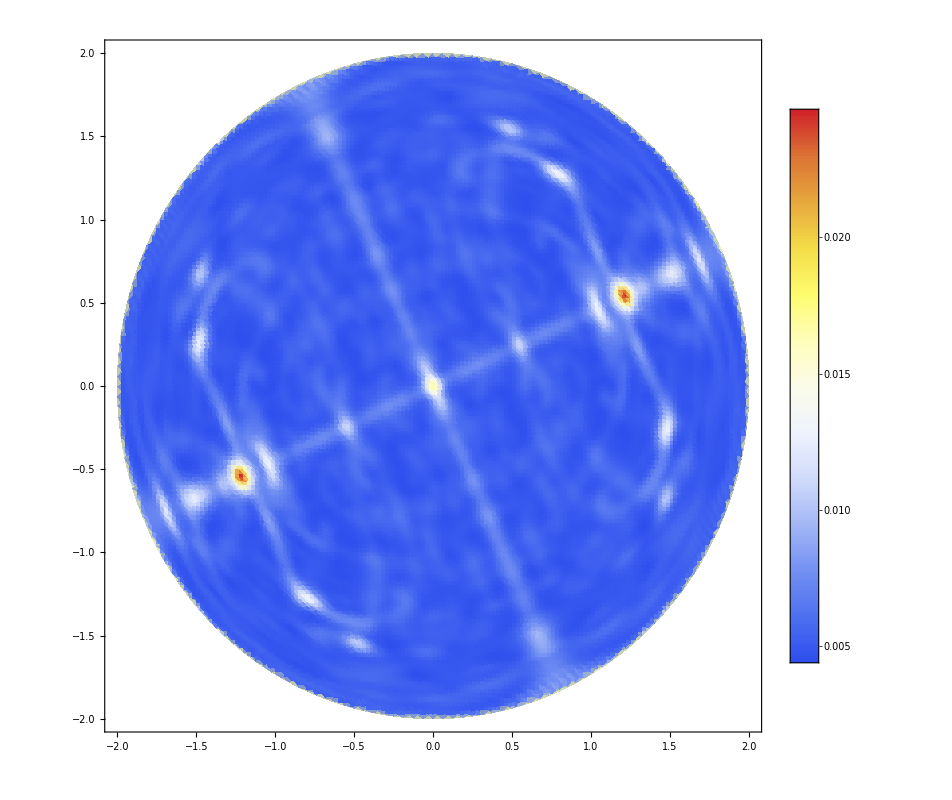

```mathematica
plots[[2]]
```